```mathematica
SetDirectory[NotebookDirectory[]];
points=Import["KM_coordinates.csv"][[2;;All]][[All,1;;2]];
pops=Import["KM_coordinates.csv"][[2;;All]][[All,3]]
callouts=Callout[#[[1]],#[[2]]]&/@Transpose[{points,Range[Length[points]]}];
ListPlot[callouts,AspectRatio->1,Frame->True, ImageSize->1500]
```

{469566,267,227328,113820,9,0,0,836,3,6,2350,3479,0,0,0,240,18,81,1520,76,76,72,216,500,112,891,42,42,36,0,0,56,1345,0,0,4764,4776,9095,4236,10489,1416,16172,4330,5454,222,4992,241692,22230,468,92176,377074,87490,68928,21090,59796,425997,532016,7935,3212,3945,445,1015,351,630,3025,6608,14000,31520,812,624,27,42,0,0,17192,16870,6144,7735,10654,9373,3630,15498,10472,1188,36,32,16,42,450,40,12800,0,0,0,1520,324,32,321,0,16,24,0,452390,17136,6,0,0,0,21,21,21,10421,27,27,40,301846,17460,19674,58144}

-Graphics-

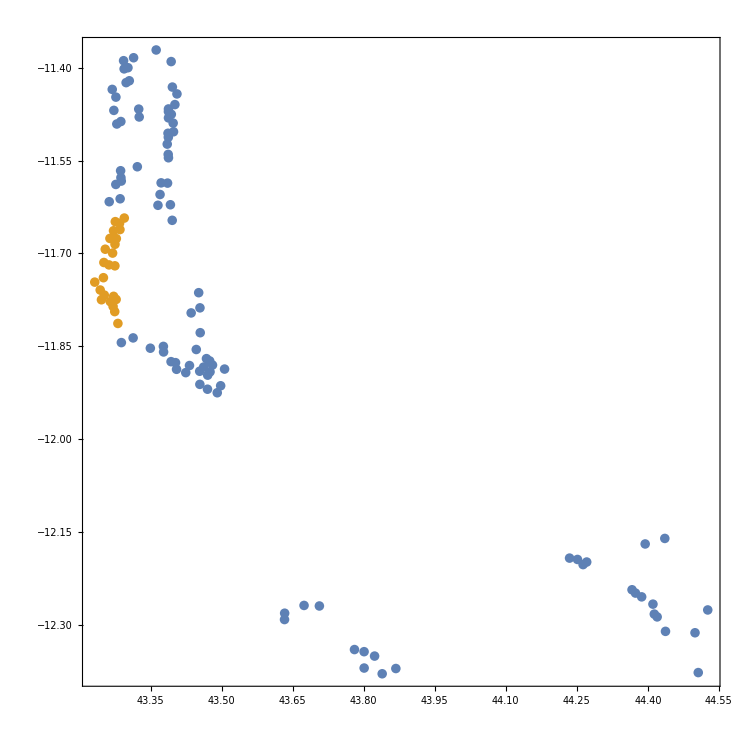

```mathematica
releaseNodes={54,53,52,4,116,47,51,1,103,58,50,60,59,61,64,63,62,65,66,67,56,3,57,55};
complementNodes=Complement[points,points[[#]]&/@releaseNodes];
ListPlot[{complementNodes,points[[#]]&/@releaseNodes}
,AspectRatio->1
,Frame->True
, ImageSize->750
]
```